# Выполнение расчетного задания #1 по курсу “Термодинамика” с вычислениями в среде Wolfram Mathematica

Маркаров М.Г.
ТФ-13-22.
Вариант 114

## Рабочее тело-бинарная смесь. 1)Аргон, μ1=39.948, ω1=0.65 2)CO2, μ2=44.011 Цикл состоит из процессов: 1-2 V-const 2-3 T-const 3-4 S-const 4-5 P-const 5-1 n=1.14

```mathematica
ω1=0.65; ω2=1-ω1;x1=(ω1/μ1)/(ω1/μ1+ω2/μ2);x2=1-x1;μ1=Quantity[39.948,("Kilograms")/("Kilomoles")];μ2=Quantity[44.011,("Kilograms")/("Kilomoles")]; p1=Quantity[1.85*10^3,"Kilopascals"];T1=Quantity[250+273.15,"Kelvins"];p2=1.35*p1;p0=Quantity[100,"Kilopascals"];v3=1.5*v1;T4=Quantity[15+273.15,"Kelvins"];
```

```mathematica
Rmolar=Quantity[8.31447,("Kilojoules")/("Kilomoles"*"Kelvins")];
```

```mathematica
R1=Rmolar/μ1
```

0.208132 kJ/(kg K)

```mathematica
R2=Rmolar/μ2
```

0.188918 kJ/(kg K)

```mathematica
R=ω1*R1 + ω2*R2
```

0.201407 kJ/(kg K)

#### Рассмотрим процесс 1-2 (V-const)

```mathematica
v1=UnitSimplify[R *T1/p1]
```

0.0569547 m^3/kg

```mathematica
v2=v1;T2=p2/p1*T1
```

706.253 K

```mathematica
UnitConvert[Quantity[706.2525,"Kelvins"],"DegreesCelsius"]
```

433.103 °C

```mathematica
{p1,v1,T1}
```

{1850. kPa,0.0569547 m^3/kg,523.15 K}

#### Найдем значения u,h,s в первой точке цикла. Сначала для каждого компонента по отдельности,потом для смеси. Значения относящиеся к компоненту 1(Ar) смеси будут заканчиваться на Ar, например удельная энтальпия аргона в точке 1 будет обозначаться как h1Ar Для аргона(Ar):

```mathematica
u1Ar=Quantity[163.3,("Kilojoules")/("Kilograms")];h1Ar=Quantity[272.2,("Kilojoules")/("Kilograms")]; s0atZeroLevelAr=Quantity[3.831,("Kilojoules")/("Kilograms"*"Kelvins")];s01Ar=Quantity[4.169,("Kilojoules")/("Kilograms"*"Kelvins")];
```

```mathematica
s1Ar=s01Ar- s0atZeroLevelAr-R1*Log[p1/p0]
```

-0.269282 kJ/(kg K)

#### Для диоксида углерода(CO2):

```mathematica
u1CO2=Quantity[326.4,("Kilojoules")/("Kilograms")];h1CO2=Quantity[425.2,("Kilojoules")/("Kilograms")]; s0atZeroLevelCO2=Quantity[4.785,("Kilojoules")/("Kilograms"*"Kelvins")];s01CO2=Quantity[5.384,("Kilojoules")/("Kilograms"*"Kelvins")];
```

```mathematica
s1CO2=s01CO2- s0atZeroLevelCO2-R2*Log[p1/p0]
```

0.0477806 kJ/(kg K)

#### Энтропия смешения смеси:

```mathematica
ΔSсмеш=Rmolar*(ω1/μ1*Log[1/x1]+ω2/μ2*Log[1/x2])
```

0.127484 kJ/(kg K)

#### u,h,s смеси в точке 1:

```mathematica
u1=ω1*u1Ar+ ω2*u1CO2
```

220.385 kJ/kg

```mathematica
h1=ω1*h1Ar+ ω2*h1CO2
```

325.75 kJ/kg

```mathematica
s1=ω1*s1Ar + ω2*s1CO2 +ΔSсмеш
```

-0.0308264 kJ/(kg K)

```mathematica
s1Check= (ω1*s01Ar+ω2*s01CO2)-(ω1*s0atZeroLevelAr+ω2*s0atZeroLevelCO2)-R*Log[p1/p0]+ΔSсмеш
```

-0.0308264 kJ/(kg K)

```mathematica
sZero=(ω1*s0atZeroLevelAr+ω2*s0atZeroLevelCO2);
```

```mathematica
{u1,h1,s1}
```

{220.385 kJ/kg,325.75 kJ/kg,-0.0308264 kJ/(kg K)}

```mathematica
{p1,v1,T1}
```

{1850. kPa,0.0569547 m^3/kg,523.15 K}

#### Найдем значения u,h,s во второй точке цикла. Отдельно по компонентам. Для диоксида углерода(CO2):

```mathematica
T2
```

706.253 K

```mathematica
UnitConvert[Quantity[706.2525,"Kelvins"],"DegreesCelsius"]
```

433.103 °C

Значение температуры не является табличным,поэтому для поиска u2,h2,s2 будем пользоваться линейной интерполяцией. Для сохранения места все приближения функций находится в другом файле.

```mathematica
u2CO2=Quantity[489.91682, "Kilojoules"/"Kilograms"];h2CO2=Quantity[623.27536, "Kilojoules"/"Kilograms"];s02CO2=Quantity[5.7079648, "Kilojoules"/("Kelvins"*"Kilograms")];
```

#### Для аргона(Ar):

```mathematica
u2Ar=Quantity[220.49296, "Kilojoules"/"Kilograms"];h2Ar=Quantity[367.51356, "Kilojoules"/"Kilograms"];s02Ar=Quantity[4.3248618, "Kilojoules"/("Kelvins"*"Kilograms")];
```

#### Значения u,h,s во второй точке цикла для смеси

```mathematica
u2=ω1*u2Ar+ω2*u2CO2
```

314.791 kJ/kg

```mathematica
h2=ω1*h2Ar+ω2*h2CO2
```

457.03 kJ/kg

```mathematica
s2=(ω1*s02Ar+ω2*s02CO2)-sZero-R*Log[p2/p0]+ΔSсмеш
```

0.123428 kJ/(kg K)

```mathematica
{u2,h2,s2}
```

{314.791 kJ/kg,457.03 kJ/kg,0.123428 kJ/(kg K)}

```mathematica
{p2,v2,T2}
```

{2497.5 kPa,0.0569547 m^3/kg,706.253 K}

#### Рассмотрим процесс 2-3 (T-const)

```mathematica
p3=p2*v2/v3
```

1665. kPa

```mathematica
T3=T2
```

706.253 K

```mathematica
{p3,v3,T3}
```

{1665. kPa,0.0854321 m^3/kg,706.253 K}

#### Найдем значения u,h,s в третьей точке цикла.Учтем что при T-const : du=0, dh=0.

```mathematica
u3=u2
```

314.791 kJ/kg

```mathematica
h3=h2
```

457.03 kJ/kg

```mathematica
s03Ar=s02Ar
```

4.32486 kJ/(kg K)

```mathematica
s03CO2=s02CO2
```

5.70796 kJ/(kg K)

```mathematica
s3=(ω1*s03Ar+ω2*s03CO2)-sZero-R*Log[p3/p0]+ΔSсмеш
```

0.205092 kJ/(kg K)

```mathematica
{u3,h3,s3}
```

{314.791 kJ/kg,457.03 kJ/kg,0.205092 kJ/(kg K)}

```mathematica
{p3,v3,T3}
```

{1665. kPa,0.0854321 m^3/kg,706.253 K}

#### Рассмотрим процесс 3-4 (S-const)

```mathematica
T4
```

288.15 K

```mathematica
UnitConvert[Quantity[288.15,"Kelvins"],"DegreesCelsius"]
```

15. °C

```mathematica
s4=s3
```

0.205092 kJ/(kg K)

```mathematica
s03=(ω1*s03Ar+ω2*s03CO2)
```

4.80895 kJ/(kg K)

Найдем  s04 каждого компонента смеси:

```mathematica
s04Ar=Quantity[3.858,("Kilojoules")/("Kilograms"*"Kelvins")];s04CO2=Quantity[4.829,("Kilojoules")/("Kilograms"*"Kelvins")];
```

```mathematica
s04=ω1*s04Ar + ω2*s04CO2
```

4.19785 kJ/(kg K)

```mathematica
p4=p3*Exp[(s04-s03)/R]
```

80.1132 kPa

```mathematica
v4=UnitSimplify[R*T4/p4]
```

0.724419 m^3/kg

```mathematica
{p4,v4,T4}
```

{80.1132 kPa,0.724419 m^3/kg,288.15 K}

#### Найдем значения u,h,s в четвертой точке цикла.Учтем что при процессе 3-4 s-const,поэтому s4=s3.Температура T4 является узлом справочной таблицы,поэтому обходимся без интерполяции для нахождения u4,h4 каждого компонента смеси.

```mathematica
T4
```

288.15 K

```mathematica
UnitConvert[Quantity[288.15,"Kelvins"],"DegreesCelsius"]
```

15. °C

```mathematica
u4CO2=Quantity[150,("Kilojoules")/("Kilograms")];h4CO2=Quantity[204.4,("Kilojoules")/("Kilograms")];u4Ar=Quantity[89.9,("Kilojoules")/("Kilograms")];h4Ar=Quantity[149.9,("Kilojoules")/("Kilograms")];
```

```mathematica
u4=ω1*u4Ar+ω2*u4CO2
```

110.935 kJ/kg

```mathematica
h4=ω1*h4Ar+ω2*h4CO2
```

168.975 kJ/kg

```mathematica
s4
```

0.205092 kJ/(kg K)

```mathematica
{u4,h4,s4}
```

{110.935 kJ/kg,168.975 kJ/kg,0.205092 kJ/(kg K)}

```mathematica
{p4,v4,T4}
```

{80.1132 kPa,0.724419 m^3/kg,288.15 K}

#### Рассмотрим процесс 4-5 (p-const) и одновременно процесс 5-1 (n=1.14)

```mathematica
p5=p4
```

80.1132 kPa

v5,T5-неизвестны.Мы можем составить систему из двух уравнений , где первое описывает процесс 4-5 Изобарный(известно v4,T4) , а второе описывает процесс 5-1 политропный(известно v1,T1,n). Такая система будет однозначно решаться относительно параметров {v5,T4}.
Первое уравнение(Изобарный процесс 4-5) :            v4/T4=v5/T5
Второе уравнение(Политропный процесс 5-1) :     T5*v5^(n-1)=T1*v1^(n-1) ; n=1.14

```mathematica
{v4,T4}
```

{0.724419 m^3/kg,288.15 K}

```mathematica
{v1,T1}
```

{0.0569547 m^3/kg,523.15 K}

```mathematica
NSolve[ξ*(0.724419/288.16*ξ)^(1.14-1)==523.15*0.0569547^(1.14-1),ξ]
```

{{ξ→355.783}}

```mathematica
T5=Quantity[355.783,"Kelvins"]
```

355.783 K

```mathematica
v5=v4*T5/T4
```

0.89445 m^3/kg

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

```mathematica
{p5,v5,T5}
```

{80.1132 kPa,0.89445 m^3/kg,355.783 K}

#### Найдем значения u,h,s в пятой точке цикла. Учтем,что T5=355.783K не является точным узлом справочной таблицы, поэтому воспользуемся линейной интерполяцией по узлам t=80°C и t=85°C.Данные об интерполяционных полиномах в отдельном файле.

#### CO2:

```mathematica
T5
```

355.783 K

```mathematica
UnitConvert[Quantity[355.783,"Kelvins"],"DegreesCelsius"]
```

82.633 °C

```mathematica
u5CO2=Quantity[195.89576000000002, "Kilojoules"/"Kilograms"]
```

195.896 kJ/kg

```mathematica
h5CO2=Quantity[263.0697, "Kilojoules"/"Kilograms"]
```

263.07 kJ/kg

```mathematica
s05CO2=Quantity[5.0118458, "Kilojoules"/("Kelvins"*"Kilograms")]
```

5.01185 kJ/(kg K)

#### Ar:

```mathematica
u5Ar=Quantity[111.04256000000001, "Kilojoules"/"Kilograms"]
```

111.043 kJ/kg

```mathematica
h5Ar=Quantity[185.06916, "Kilojoules"/"Kilograms"]
```

185.069 kJ/kg

```mathematica
s05Ar=Quantity[3.9676862, "Kilojoules"/("Kelvins"*"Kilograms")]
```

3.96769 kJ/(kg K)

#### Найдем u,h,s смеси в точке 5 цикла

```mathematica
u5=ω1*u5Ar+ω2*u5CO2
```

140.741 kJ/kg

```mathematica
h5=ω1*h5Ar+ω2*h5CO2
```

212.369 kJ/kg

```mathematica
s5=(ω1*s05Ar+ω2*s05CO2)-sZero-R*Log[p5/p0]+ΔSсмеш
```

0.340384 kJ/(kg K)

```mathematica
{u5,h5,s5}
```

{140.741 kJ/kg,212.369 kJ/kg,0.340384 kJ/(kg K)}

```mathematica
{p5,v5,T5}
```

{80.1132 kPa,0.89445 m^3/kg,355.783 K}

#### Сведем все результаты вычислений в одну таблицу {p,v,T,u,h,s}

```mathematica
p={p1,p2,p3,p4,p5};v={v1,v2,v3,v4,v5};T={T1,T2,T3,T4,T5};u={u1,u2,u3,u4,u5};h={h1,h2,h3,h4,h5};s={s1,s2,s3,s4,s5};
```

```mathematica
Insert[ReplacePart[Grid[Transpose[{Range[5],p,v,T,u,h,s}]],1->Prepend[First[Insert[Grid[Transpose[{Range[5],p,v,T,u,h,s}],Frame->True],{Dividers->All,Spacings->1.5 {1,1}},2]],{"Точка цикла","p","v","T","u","h","s"}]],{Dividers->All,Spacings->1.5 {1,1}},2]
```

Точка цикла | p | v | T | u | h | s
1 | 1850. kPa | 0.0569547 m^3/kg | 523.15 K | 220.385 kJ/kg | 325.75 kJ/kg | -0.0308264 kJ/(kg K)
2 | 2497.5 kPa | 0.0569547 m^3/kg | 706.253 K | 314.791 kJ/kg | 457.03 kJ/kg | 0.123428 kJ/(kg K)
3 | 1665. kPa | 0.0854321 m^3/kg | 706.253 K | 314.791 kJ/kg | 457.03 kJ/kg | 0.205092 kJ/(kg K)
4 | 80.1132 kPa | 0.724419 m^3/kg | 288.15 K | 110.935 kJ/kg | 168.975 kJ/kg | 0.205092 kJ/(kg K)
5 | 80.1132 kPa | 0.89445 m^3/kg | 355.783 K | 140.741 kJ/kg | 212.369 kJ/kg | 0.340384 kJ/(kg K)

#### Расчет теплоты,работы и средней температуры подвода тепла в каждом процессе

#### Процесс 1-2: V-const

```mathematica
Δu12=u2-u1
```

94.4063 kJ/kg

```mathematica
Δh12=h2-h1
```

131.28 kJ/kg

```mathematica
Δs12=s2-s1
```

0.154255 kJ/(kg K)

```mathematica
l12=0;q12=Δu12
```

94.4063 kJ/kg

```mathematica
T12=q12/Δs12
```

612.016 K

#### Процесс 2-3: T-const

```mathematica
Δu23=u3-u2
```

0. kJ/kg

```mathematica
Δh23=h3-h2
```

0. kJ/kg

```mathematica
Δs23=s3-s2
```

0.0816636 kJ/(kg K)

```mathematica
T23=T2
```

706.253 K

```mathematica
q23=T23*Δs23
```

57.6751 kJ/kg

```mathematica
l23=q23
```

57.6751 kJ/kg

#### Процесс 3-4: S-const

```mathematica
Δu34=u4-u3
```

-203.856 kJ/kg

```mathematica
Δh34=h4-h3
```

-288.055 kJ/kg

```mathematica
Δs34=s4-s3
```

0. kJ/(kg K)

```mathematica
l34=-Δu34
```

203.856 kJ/kg

```mathematica
q34=Quantity[0,("Kilojoules")/("Kilograms")]
```

0 kJ/kg

```mathematica
T34=Quantity[0,"Kelvins"]
```

0 K

#### Процесс 4-5: P-const

```mathematica
Δu45=u5-u4
```

29.8062 kJ/kg

```mathematica
Δh45=h5-h4
```

43.3943 kJ/kg

```mathematica
Δs45=s5-s4
```

0.135292 kJ/(kg K)

```mathematica
q45=Δh45
```

43.3943 kJ/kg

```mathematica
l45=q45-Δu45
```

13.5882 kJ/kg

```mathematica
T45=q45/Δs45
```

320.746 K

#### Процесс 5-1: n=1.14 , n-const

```mathematica
n=1.14
```

1.14

```mathematica
Δu51=u1-u5
```

79.6438 kJ/kg

```mathematica
Δh51=h1-h5
```

113.381 kJ/kg

```mathematica
Δs51=s1-s5
```

-0.37121 kJ/(kg K)

```mathematica
l51=R*(T5-T1)/(n-1)
```

-240.778 kJ/kg

```mathematica
q51=l51+Δu51
```

-161.134 kJ/kg

```mathematica
T51=q51/Δs51
```

434.078 K

#### Составим таблицу {Δu,Δh,Δs,l,q,T̄}

```mathematica
Δu={Δu12,Δu23,Δu34,Δu45,Δu51,ΣΔu};Δh={Δh12,Δh23,Δh34,Δh45,Δh51,ΣΔh};Δs={Δs12,Δs23,Δs34,Δs45,Δs51,ΣΔs};l={l12,l23,l34,l45,l51,Σl};q={q12,q23,q34,q45,q51,Σq};
Tmid={T12,T23,T34,T45,T51,{TmidNEG,
TmidPOS}};
```

```mathematica
Magnify[Insert[ReplacePart[Grid[Transpose[{{12,23,34,45,51,"Цикл"},Δu,Δh,Δs,l,q,Tmid}]],1->Prepend[First[Grid[Transpose[{{12,23,34,45,51,"Цикл"},Δu,Δh,Δs,l,q,Tmid}]]],{"Процесс","Δu","Δh","Δs","l","q","Tmid"}]],{Dividers->All,Spacings->1.5 {1,1}},2],0.8]
```

Процесс | Δu | Δh | Δs | l | q | Tmid
12 | 94.4063 kJ/kg | 131.28 kJ/kg | 0.154255 kJ/(kg K) | 0 | 94.4063 kJ/kg | 612.016 K
23 | 0. kJ/kg | 0. kJ/kg | 0.0816636 kJ/(kg K) | 57.6751 kJ/kg | 57.6751 kJ/kg | 706.253 K
34 | -203.856 kJ/kg | -288.055 kJ/kg | 0. kJ/(kg K) | 203.856 kJ/kg | 0 kJ/kg | 0 K
45 | 29.8062 kJ/kg | 43.3943 kJ/kg | 0.135292 kJ/(kg K) | 13.5882 kJ/kg | 43.3943 kJ/kg | 320.746 K
51 | 79.6438 kJ/kg | 113.381 kJ/kg | -0.37121 kJ/(kg K) | -240.778 kJ/kg | -161.134 kJ/kg | 434.078 K
Цикл | 0. kJ/kg | 2.84217×10^-14 kJ/kg | 0. kJ/(kg K) | 34.3415 kJ/kg | 34.3415 kJ/kg | {434.078 K,526.59 K}

#### Полный цикл

```mathematica
ΣΔu=Δu12+Δu23+Δu34+Δu45+Δu51
```

0. kJ/kg

```mathematica
ΣΔh=Δh12+Δh23+Δh34+Δh45+Δh51
```

2.84217×10^-14 kJ/kg

```mathematica
ΣΔs=Δs12+Δs23+Δs34+Δs45+Δs51
```

0. kJ/(kg K)

```mathematica
Σq=q12+q23+q34+q45+q51
```

34.3415 kJ/kg

```mathematica
Σl=l12+l23+l34+l45+l51
```

34.3415 kJ/kg

```mathematica
ΣqPOS=q12+q23+q45
```

195.476 kJ/kg

```mathematica
ΣΔsPOS=Δs12+Δs23+Δs45
```

0.37121 kJ/(kg K)

#### Температура при подводе тепла:

```mathematica
TmidPOS=ΣqPOS/ΣΔsPOS
```

526.59 K

```mathematica
ΣqNEG=q51
```

-161.134 kJ/kg

```mathematica
ΣΔsNEG=Δs51
```

-0.37121 kJ/(kg K)

#### Температура при отводе тепла:

```mathematica
TmidNEG=ΣqNEG/ΣΔsNEG
```

434.078 K

#### Термический КПД цикла:

```mathematica
η=Σl/ΣqPOS
```

0.175682

```mathematica
T
```

{523.15 K,706.253 K,706.253 K,288.15 K,355.783 K}

```mathematica
s
```

{-0.0308264 kJ/(kg K),0.123428 kJ/(kg K),0.205092 kJ/(kg K),0.205092 kJ/(kg K),0.340384 kJ/(kg K)}

```mathematica
Ts=Range[Length[T]];
```

```mathematica
For[i=1,i<=Length[T],i++,Ts[[i]]={T[[i]],s[[i]]}]
```

```mathematica
Ts
```

{{523.15 K,-0.0308264 kJ/(kg K)},{706.253 K,0.123428 kJ/(kg K)},{706.253 K,0.205092 kJ/(kg K)},{288.15 K,0.205092 kJ/(kg K)},{355.783 K,0.340384 kJ/(kg K)}}

```mathematica
TsPlot=Show[Show[ListLinePlot[{Ts,{{Quantity[523.15, "Kelvins"],Quantity[-0.030826448130162984, ("Kilojoules")/("Kelvins" "Kilograms")]},{Quantity[355.783, "Kelvins"],Quantity[0.3403838397541039, ("Kilojoules")/("Kelvins" "Kilograms")]}}},PlotTheme->"Scientific",InterpolationOrder->1,PlotStyle->Gray,PlotMarkers->{Automatic,14}],Axes->True,AxesStyle->Black],AxesLabel->{RawBoxes[RowBox[{"T",","," ","Kelvin"}]],RawBoxes[RowBox[{"s",","," ",RowBox[{"kJ","/",RowBox[{"(",RowBox[{"kg","*","K"}],")"}]}]}]]},PlotLabel->HoldForm[T-s диаграмма цикла],LabelStyle->{GrayLevel[0],Italic}];
```

```mathematica
marker1=Graphics[Text["1",{523.15,-0.0308264},{-5,0}]];
marker2=Graphics[Text["2",{706.253,0.123428},{+5,0}]];
marker3=Graphics[Text["3",{706.253,0.205092},{+4,-0.7}]];
marker4=Graphics[Text["4",{288.15,0.205092},{5,0}]];
marker5=Graphics[Text["5",{355.783,0.340384},{-5,0}]];
```

#### T-s диаграмма цикла

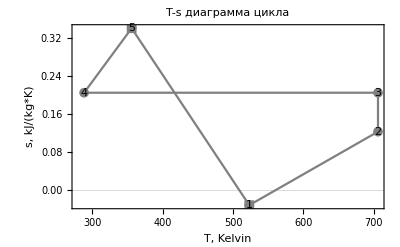

Set::write: Tag Plus in -1.14+5 is Protected.

```mathematica
Show[Show[Show[ListLinePlot[{Ts,{{Quantity[523.15, "Kelvins"],Quantity[-0.030826448130162984, ("Kilojoules")/("Kelvins" "Kilograms")]},{Quantity[355.783, "Kelvins"],Quantity[0.3403838397541039, ("Kilojoules")/("Kelvins" "Kilograms")]}}},PlotTheme->"Scientific",InterpolationOrder->1,PlotStyle->Gray,PlotMarkers->{Automatic, 10},PlotLegends->"1-2  v-Const

2-3  T-Const

3-4 s-Const

4-5 p-Const 

5-1 n=1.14"],Axes->True,AxesStyle->Black],AxesLabel->{RawBoxes[RowBox[{"T",","," ","Kelvin"}]],RawBoxes[RowBox[{"s",","," ",RowBox[{"kJ","/",RowBox[{"(",RowBox[{"kg","*","K"}],")"}]}]}]]},PlotLabel->HoldForm[T-s диаграмма цикла],LabelStyle->{GrayLevel[0],Italic}],marker1,marker2,marker3,marker4,marker5]
```

#### Диаграмму цикла в p-v координатах построим с применением пакета Matlab, см. приложение